### Supplementary code for simulations of D. suzukii population dynamics in “Large-scale open field trials in California and Oregon to evaluate the potential use of a new behavioral control system for Drosophila suzukii Matsumura (Diptera: Drosophilidae)” by Tait et al. (2022) Contact for code: ferdinand.pfab@gmail.com This file runs the simulations. Important: run weather_aurora.nb and parameter_fits_blueberry.nb before.

```mathematica
(*output directory for plots*)
directory=NotebookDirectory[];
(*parameters*)
(*sex ratio*)
Πs=1/2;
(*fecundity of females*)
β[c_]:= gauss[c]/.fitfecundity;
(*mortality of juvenile stages*)
δv[c_]:= gaussinv[c]/.fitjmort;
(*mortality of egg stage*)
δe[c_]:=δv[c];
(*mortality of larval stage*)
δl[c_]:=δv[c];
(*mortality of pupal stage*)
δp[c_]:=δv[c];
(*number of substages of egg, larval, pupal and adult stages*)
ke=15;kl=25;kp=25;ka=4;
(*initial number of individuals*)
a0=2;
(*maturation speeds of egg, larvae, pupae and adults. Note: adult "maturation" means they die*)
ge[c_]:=ke/gaussinv[c]/.fitetol;
gl[c_]:=ke/gaussinv[c]/.fitltop;
gp[c_]:=kp/gaussinv[c]/.fitptoa;
ga[c_]:=ka/gauss[c]/.fitatom;
(*state variables: egg, larvae, pupae and adults. These are all vectors by themselves, including the substages*)
vars={e,l,p,a};
(*matrices for transitions between stages and substages*)
(*maturation between substages*)
mM[k_]:=SparseArray[Band[{2,1},{k,k-1},{1,1}]->1,{k,k}]-SparseArray[Band[{1,1},{k,k},{1,1}]->1,{k,k}];
(*maturation between stages*)
mS[k1_,k2_]:=SparseArray[{1,k2}->1,{k1,k2}];
(*fecundity: adults create new individuals in first egg substage*)
mF[k1_,k2_]:=SparseArray[Band[{1,1},{1,k2},{0,1}]->1,{k1,k2}];
(*vector to sum up all substages of a stage*)
vC[k_]:=Table[1,k];
(*start time of simulation*)
tmin=30;
(*end time of simulation*)
tmax=90;
(*function to run simulations*)
(*interventions = pesticide interventions, as defined below*)
(*fecundity is multiplied by βfactor, this is used to reduce the fecundity in the gum treatments (as eggs laid in gum do not develope)*)
sim[interventions_,tmin_,tmax_,βfactor_]:=
Module[{eqs,inis,μl,γ},
(*this is the fecundity at time t, taken into account the sex rartio*)
γ[t_]:=Πs βfactor β[w[t]] ;
(*differential equations, note that the state variables are vectors with the substages*)
eqs=
{
e'[t]==γ[t] mF[ke,ka].a[t]+ge[w[t]] mM[ke].e[t]-δe[w[t]]e[t],
l'[t]==ge[w[t]] mS[kl,ke].e[t]+gl[w[t]] mM[kl].l[t]-δl[w[t]] l[t],
p'[t]==gl[w[t]] mS[kp,kl].l[t]+gp[w[t]] mM[kp].p[t]-δp[w[t]] p[t],
a'[t]==gp[w[t]] mS[ka,kp].p[t]+ga[w[t]] mM[ka].a[t]
};
(*initial conditions, start with only adults. Those adults are distributed uniformly over the adult substages*)
inis={
e[tmin]==Table[0,ke],
l[tmin]==Table[0,kl],
p[tmin]==Table[0,kp],
a[tmin]==Table[a0/ka,ka]
};
(*solve the ODEs numerically*)
NDSolve[
Flatten[{
eqs,
inis,
interventions
}],
vars,
{t,tmin,tmax}
]];
```

```mathematica
(*colors for different stages*)
colorselpa=ColorData[97]/@{2,3,4,1};
legend=Grid[Transpose[{Plot[.5,{x,0,1},PlotStyle->{#,Thickness[.1]},Axes->None,PlotRange->{0,1},ImageSize->25]&/@colorselpa,Style[#,16]&/@{"Eggs","Larvae","Pupae","Adults"}}],Alignment->Left]
```

-Graphics- | Eggs
-Graphics- | Larvae
-Graphics- | Pupae
-Graphics- | Adults

```mathematica
(*gum efficiency from Tait et al 2018, reduction of eggs in fruit close by (solid) gum*)
gumefficiency=14/28.7;

(*function to plot the simulations*)
mkplot[applications_,min_,max_,title_,tmin_,tmax_,tminplot_,logornot_,βfactor_]:=
Module[{sol,intervene,
timings=applications},
intervene=Module[{why},Table[
why[t==timings[[i]],Evaluate@Table[stage[t]->(1-(stage/.pesticideefficiencystagewise))stage[t],{stage,{a,e,l,p}}](*{a[t],e[t],l[t],p[t]}->{a[t],e[t],l[t],p[t]}*)],
{i,Length[timings]}]/.why->WhenEvent];
sol=sim[intervene,(*fruit,*)tmin,tmax,βfactor];
Grid[{{
logornot[Evaluate[Flatten[{Table[vC[{ke,kl,kp,ka}[[i]]].({e,l,p,a}[[i]][t]/.sol[[1]]),{i,4}](*/a0*)
}]],{t,tminplot,tmax},PlotRange->{Automatic,{min,max}},
PlotLabel->title,
PlotStyle->Table[{col,Thickness[.008]},{col,colorselpa}],LabelStyle->20,
Frame->{{True,True},{True,True}},
ImagePadding->{{80,20},{50,30}},
PlotRangePadding->0,
ImageSize->500, 
FrameTicks->{{Automatic,None},{xlabelsmonth,
Table[{timings[[i]],Style["",Bold,14],
{Scaled[.2],Scaled[.00002]},{Dashed,Thick}},{i,Length[timings]}]}}
],
legend
}},Alignment->Left]
];
```

```mathematica
(*do the plots*)
```

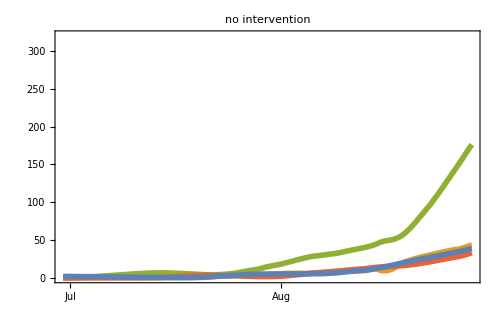
-Graphics- | -Graphics- | Eggs
-Graphics- | Larvae
-Graphics- | Pupae
-Graphics- | Adults

```mathematica
(Export[directory<>"sim-no-intervention-blueberry.pdf",#];#)&@mkplot[{},0,320,"no intervention",tmin,tmax,tmin,Plot,1]
```

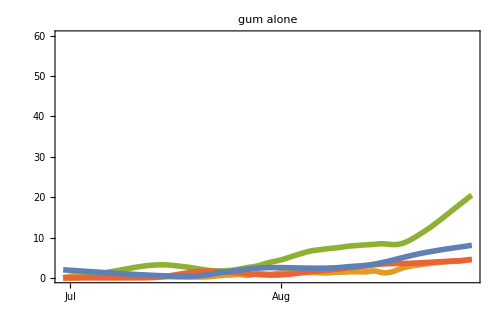
-Graphics- | -Graphics- | Eggs
-Graphics- | Larvae
-Graphics- | Pupae
-Graphics- | Adults

```mathematica
(Export[directory<>"sim-gum-alone-blueberry.pdf",#];#)&@mkplot[{},0,60,"gum alone",tmin,tmax,tmin,Plot,gumefficiency]
```

```mathematica
(*times of insecticide applications*)
interventiontimes=(30+7Range[4])[[{1,4}]];
(*pesticide efficiencies on the life stages from Mermet et al 2020 on spinosad, lab experiments, table 2*)
pesticideefficiencystagewise={e->.828,l->.759,p->.997,a->.948};
```

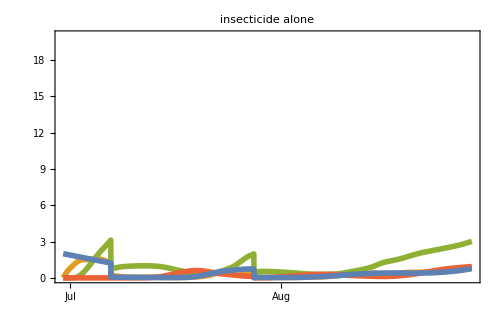
-Graphics- | -Graphics- | Eggs
-Graphics- | Larvae
-Graphics- | Pupae
-Graphics- | Adults

```mathematica
(Export[directory<>"sim-pesticide-alone-blueberry.pdf",#];#)&@mkplot[interventiontimes,0, 20,"insecticide alone",tmin,tmax,tmin,Plot,1]
```

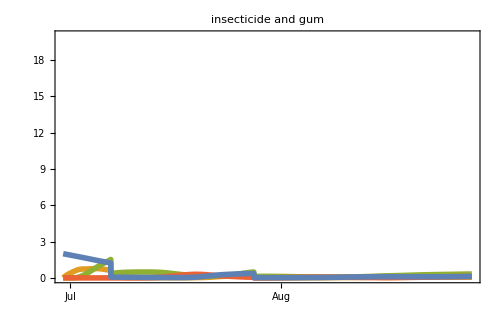
-Graphics- | -Graphics- | Eggs
-Graphics- | Larvae
-Graphics- | Pupae
-Graphics- | Adults

```mathematica
(Export[directory<>"sim-gum-and-pesticide-blueberry.pdf",#];#)&@mkplot[interventiontimes,0, 20,"insecticide and gum",tmin,tmax,tmin,Plot,gumefficiency]
```